# Electroweak baryogenesis at high wall velocities (arXiv:2001.00568)

## Master Code Reformulated

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
SetOptions[{ParametricPlot,ListLinePlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot,ListContourPlot,LogPlot,Plot,RegionPlot,ContourPlot},Frame->True,BaseStyle->{FontColor->Black,FontWeight->"Normal",FontSize->16,FontFamily->"Times"},Axes->False,PlotLegends->Automatic,AspectRatio->1,ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->Full];
colours=ColorData[97,"ColorList"];
WP=MachinePrecision;
(*******************************************************************************************************************)
(**********************************************************************************************)
```

```mathematica
(*gtab=Import["standardmodel2018.txt","Table",HeaderLines->8][[;;;;20]];*)
gtab=Import["./satoshi_dof.dat","Table",HeaderLines->8][[;;;;20]];
gstar[T_]:=Interpolation[gtab[[All,{1,2}]]][T];
gsstar[T_]:=Interpolation[gtab[[All,{1,4}]]][T];
(*****************************************************************************************************)
(*****************************************************************************************************)
```

```mathematica
params3=Import["SCANS/Z2_breaking_sols.csv","Dataset","HeaderLines"->1];
```

```mathematica
Tnlist=params3[All,"Tnuc_0"];
TpoverTnlist=params3[All,"Tp/TN"];
vwlist=params3[All,"vw"];
vplist=params3[All,"vp"];
h0list=params3[All,"h0"];
Lhlist=params3[All,"Lh"];
Lslist=params3[All,"Ls"];
dslist=params3[All,"ds"];
shighlist=params3[All,"shigh"];
slowlist=params3[All,"slow"];
alphalist=params3[All,"alpha_max"];
(*alphalist=params3[All,"alpha"];
betalist=params3[All,"d/dT(S_3/T)"];*)
```

```mathematica
vwlist[[1]]
```

```mathematica
MasterFunction[Tn_,vw_,h0_,Lh_,sl_,sh_,Ls_,ds_,ΛCP_,Infty_,points_]:=MasterFunction[Tn,vw,h0,Lh,sl,sh,Ls,ds,ΛCP,Infty,points]=Module[{ηobs=8 10^-11,β=1/Tn,Γsph=10^-6 Tn,h,s,mt,Bond,Equation,sol,μtlsol,μtrsol,μblsol,μhsol,μBL,fsph,gdof,ηB,Plot1,Plot2,
ΓSS=4.9*10^-4 Tn,
Γy=4.2*10^-3 Tn,Dq=6/Tn(*quark diffusion constant*),
Dh=20/Tn(*higgs diffusion constant*),
inf=Infty Lh (*defines the region of interpolation/integration*)},
pw=√(w^2-x^2);(*Formula defined after A3*)
pz=1/(√(1-vw^2))(y pw-w vw);(*Formula defined after A3*)
Eb=1/(√(1-vw^2))(w-vw y pw);(*Formula defined after A3*)
Vs = √(pz^2)/√(pz^2+x^2);(*Formula  A4*)
Vh=Vs^2 1/(√(1-x^2/Eb^2));(*Formula  A5*);
ff=1/(Exp[β w]+1);(*Distribution funcion for fermion *)
fb=1/(Exp[β w]-1);(*Distribution funcion for boson *)
ff1=D[ff,w];(*Derivative of Distribution funcion for fermion *)
fb1=D[fb,w];(*Derivative of Distribution funcion for boson *)
ff2=D[ff1,w];(*Second Derivative of Distribution funcion for fermion *)
fb2=D[fb1,w];(*Second Derivative of Distribution funcion for boson *)
h[z_]:=h0/2(Tanh[z/Lh]+1);(**equation (50) LEFT MOVING WALL!!**)
(*s[z_]:=s0/2(1-Tanh[z/Ls-ds]);*)(**equation (50)**)
s[z_]:=(sl-sh)/2 Tanh[z/Ls-ds]+(sl+sh)/2;
mt[z_]:=0.99571/(√2) h[z] √(1+s[z]^2/ΛCP^2);(**equation (49)**)
θ[z_]:=ArcTan[s[z]/ΛCP];(**equation (49)**)
mb[z_]:=4.2*h[z]/h0 ;
mh[z_]:=125.3*h[z]/h0 ;
Γm[z_]:=mt[z]^2/(63 Tn);
mW[z_]:=0.65 h[z]/2 (*W boson mass*);
Γh[z_]:=mW[z]^2/(50Tn);
Xmax=Max[{mt[inf],mh[inf],mb[inf],mW[inf]}]+0.1(*Max value of x used for interpolating coefficient functions*);Kf0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2 NIntegrate[pw Eb ff/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for fermions*);
Kb0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for bosons*);
Kf0inter=Interpolation[Table[{x,Kf0[x,vw]},{x,0,Xmax,Xmax/10}]];
Kb0inter=Interpolation[Table[{x,Kb0[x,vw]},{x,0,Xmax,Xmax/10}]];
K0t[z_]:=Kf0inter[mt[z]];
K0b[z_]:=Kf0inter[mb[z]];
K0h[z_]:=Kb0inter[mh[z]];Df0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=0*);
Db0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=0*);Df0inter=Interpolation[Table[{x,Df0[x,vw]},{x,0,Xmax,Xmax/10}]];
Db0inter=Interpolation[Table[{x,Db0[x,vw]},{x,0,Xmax,Xmax/10}]];
D0t[z_]:=Df0inter[mt[z]];
D0b[z_]:=Df0inter[mb[z]];
D0h[z_]:=Db0inter[mh[z]];Df1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=1*);
Db1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=1*);
Df1inter=Interpolation[Table[{x,Df1[x,vw]},{x,0,Xmax,Xmax/10}]];
Db1inter=Interpolation[Table[{x,Db1[x,vw]},{x,0,Xmax,Xmax/10}]];
D1t[z_]:=Df1inter[mt[z]];
D1b[z_]:=Df1inter[mb[z]];
D1h[z_]:=Db1inter[mh[z]];Df2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=2*);
Db2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=2*);Df2inter=Interpolation[Table[{x,Df2[x,vw]},{x,0,Xmax,Xmax/10}]];
Db2inter=Interpolation[Table[{x,Db2[x,vw]},{x,0,Xmax,Xmax/10}]];
D2t[z_]:=Df2inter[mt[z]];
D2b[z_]:=Df2inter[mb[z]];
D2h[z_]:=Db2inter[mh[z]];Qf1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[pw  ff2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞}](*Formula (27) for fermions, l=1*);
Qb1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[pw  fb2/.{x->0,vvw->vi},{y,-1,1}],{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw  fb2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞},WorkingPrecision->10]](*Formula (27) for bosons, l=1*);
Qf1inter=Interpolation[Table[{x,Qf1[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb1inter=Interpolation[Table[{x,Qb1[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1t[z_]:=Qf1inter[mt[z]];
Q1b[z_]:=Qf1inter[mb[z]];
Q1h[z_]:=Qb1inter[mh[z]];
Qf2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[(pw pz)/Eb ff2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10](*Formula (27) for fermions, l=2*);
Qb2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{y,-1,1}],{w,xi,∞,xi},Method->PrincipalValue],NIntegrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (27) for bosons, l=2*);Qf2inter=Interpolation[Table[{x,Qf2[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb2inter=Interpolation[Table[{x,Qb2[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2t[z_]:=Qf2inter[mt[z]];
Q2b[z_]:=Qf2inter[mb[z]];
Q2h[z_]:=Qb2inter[mh[z]];
Q1fo8integrand=FullSimplify[(Integrate[pw/pz Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh ff1/.{x->0,vw->vi},y]/.{y->-1})];Q1bo8integrand=FullSimplify[(Integrate[pw/pz Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh fb1/.{x->0,vw->vi},y]/.{y->-1})];Q1fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=1, helicity eigenstates*);
Q1bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=1, helicity eigenstates*);Q1fo8inter=Interpolation[Table[{x,Q1fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1bo8inter=Interpolation[Table[{x,Q1bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o8t[z_]:=Q1fo8inter[mt[z]];
Q1o8b[z_]:=Q1fo8inter[mb[z]];
Q1o8h[z_]:=Q1bo8inter[mh[z]];Q2fo8integrand=FullSimplify[(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->-1})];Q2bo8integrand=FullSimplify[(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=2, helicity eigenstates*);
Q2bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=2, helicity eigenstates*);Q2fo8inter=Interpolation[Table[{x,Q2fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2bo8inter=Interpolation[Table[{x,Q2bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2o8t[z_]:=Q2fo8inter[mt[z]];
Q2o8b[z_]:=Q2fo8inter[mb[z]];
Q2o8h[z_]:=Q2bo8inter[mh[z]];
Q1fo9integrand=FullSimplify[(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q1fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q1fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (41), l=1, helicity eigenstates*);Q1fo9nter=Interpolation[Table[{x,Q1fo9[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o9t[z_]:=Q1fo9nter[mt[z]];
Q1o9b[z_]:=Q1fo9nter[mb[z]];
Q2fo9integrand=FullSimplify[(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q2fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->15]](*Formula (41) for fermions, l=2, helicity eigenstates*);Q2fo9inter=Interpolation[Table[{x,Q2fo9[x,vw]},{x,0,Xmax,Xmax/10}]];Q2o9t[z_]:=Q2fo9inter[mt[z]];
Q2o9b[z_]:=Q2fo9inter[mb[z]];
St1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q1o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q1o9t[z])/.{z->zz}];Sb1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q1o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q1o9b[z])/.{z->zz}];St2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q2o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q2o9t[z])/.{z->zz}];Sb2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q2o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q2o9b[z])/.{z->zz}];
Γhtot[z_]:=D2h[z]/(Dh D0h[z])(*W scattering rate. This was not provided in the paper and we took it directly from ref [47] 0605242*);Γttot[z_]:=D2t[z]/(Dq D0t[z]);
Γbtot[z_]:=D2b[z]/(Dq D0b[z]);
δCtL1[z_]:=β K0t[z] (Γy(μtl[z]-μtr[z]+μh[z])+Γm[z](μtl[z]-μtr[z])+Γhtot[z](μtl[z]-μbl[z])+ ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]))(*Formula (53), we divide by T to get dimensions right*);δCtL2[z_]:=(-Γttot[z]utl[z]-vw δCtL1[z]);
δCbL1[z_]:=β K0b[z](Γy(μbl[z]-μtr[z]+μh[z])+Γhtot[z](μbl[z]-μtl[z])+ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));δCbL2[z_]:=(-Γbtot[z]ubl[z]-vw δCbL1[z]);δCtR1[z_]:=β K0t[z](-Γy(μtl[z]+μbl[z]-2μtr[z]+2μh[z])-Γm[z](μtl[z]-μtr[z])-ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));
δCtR2[z_]:=(-Γttot[z]utr[z]-vw δCtR1[z]);
δCh1[z_]:=β K0h[z]( Γy (μtl[z]+μbl[z]-2μtr[z]+2μh[z])+Γh[z] μh[z]);
δCh2[z_]:=(-Γhtot[z]uh[z]-vw δCh1[z]);
{htl,htr,hbl}={-1,1,-1};TopLeft1={-D1t[z] μtl'[z]+utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q1t[z] μtl[z]-δCtL1[z]==htl St1[z]};TopLeft2={-D2t[z] μtl'[z]-vw utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtl[z]-δCtL2[z]== htl St2[z]};
BottomLeft1={-D1b[z] μbl'[z]+ubl'[z]+ D[(mb[z])^2,z] vw/(√(1-vw^2))Q1b[z] μbl[z]-δCbL1[z]==hbl Sb1[z]};BottomLeft2={-D2b[z] μbl'[z]-vw ubl'[z]+D[(mb[z])^2,z] vw/(√(1-vw^2)) Q2b[z] μbl[z]-δCbL2[z]==hbl Sb2[z]};TopRight1={-D1t[z] μtr'[z]+utr'[z]+ D[(mt[z])^2,z] vw/(√(1-vw^2))Q1t[z] μtr[z]-δCtR1[z]==htr St1[z]};TopRight2={-D2t[z] μtr'[z]-vw utr'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtr[z]-δCtR2[z]==htr St2[z]};Higgs1={-D1h[z] μh'[z]+uh'[z]+ D[(mh[z])^2,z] vw/(√(1-vw^2))Q1h[z] μh[z]-δCh1[z]==0};
Higgs2={-D2h[z] μh'[z]-vw uh'[z]+D[(mh[z])^2,z] vw/(√(1-vw^2)) Q2h[z] μh[z]-δCh2[z]==0};
Bond={ μtl[inf]==0,μtr[inf]==0,μbl[inf]==0,μh[inf]==0, μtl[-inf]==0,μtr[-inf]==0,μbl[-inf]==0,μh[-inf]==0};Equation=Join[TopLeft1,TopLeft2,TopRight1,TopRight2,BottomLeft1,BottomLeft2,Higgs1,Higgs2,Bond];sol=NDSolve[Equation,{μtl,μtr,μbl,μh, utl,utr,ubl,uh},{z,-inf,inf},Method->{"Shooting",Method->{"FixedStep",Method->"ExplicitEuler"}},StartingStepSize->2inf/points(*,Method->{"Shooting",Method->"StiffnessSwitching"},MaxStepSize->0.01*)];μtlsol[z_]:=μtl[z]/.sol[[1]][[1]];μtrsol[z_]:=μtr[z]/.sol[[1]][[2]];μblsol[z_]:=μbl[z]/.sol[[1]][[3]];μhsol[z_]:=μh[z]/.sol[[1]][[4]];μBL[z_]:=1/2(1+4D0t[z])μtlsol[z]+1/2(1+4D0b[z])μblsol[z]+2 D0t[z] μtrsol[z];
fsph[z_]:=Min[{1,2.5 Tn/Γsph Exp[-40 h[z]/Tn]}];
gdof=gstar[Tn](*106.75*);
ηB=405 Γsph/(4π^2 vw gdof Tn)√(1-vw^2) NIntegrate[μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[vw])(*√(1-vw^2)*)],{z,-inf,inf},Method->"QuasiMonteCarlo",AccuracyGoal->2,PrecisionGoal->2];
Plot2=Plot[405 Γsph/(4π^2 vw gdof Tn)√(1-vw^2)μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[vw])(*√(1-vw^2)*)]/ηobs,{z,-inf,inf},FrameLabel->{"z","dη/ηobs"},PlotRange->All];
Plot1=Plot[{μtlsol[z] β,μblsol[z] β,μhsol[z] β,μtrsol[z]β},{z,-inf,inf},PlotRange->Full,PlotLegends->{"t_L"," b_L"," μ_h","t_R"},PlotLabel->Subscript[v, w]==-vw,FrameLabel->{"z",""},PlotRange->All];
(*Return[Abs[ηB/ηobs]];*)
Return[{Plot1,Plot2,Abs[ηB/ηobs]}];
];
```

```mathematica
(*MasterOutputOld[i_,Λcutoff_,Infty_,points_]:=MasterFunction[Tnlist[[i]],-vwlist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],,shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,Infty,points];*)
```

```mathematica
MasterPars[i_]:=Print[ "Pars α=",alphalist[[i]],(*" β/H=",betalist[[i]],*)" T_n=",Tnlist[[i]]," v_w=",vwlist[[i]]," T_p=",Tnlist[[i]]*TpoverTnlist[[i]]," v_p=",vplist[[i]]," h_0=",h0list[[i]]," L_h=",Lhlist[[i]]," s_l=",slowlist[[i]]," s_h=",shighlist[[i]]," L_s=",Lslist[[i]]," ds=",dslist[[i]]];
```

```mathematica
MasterPars[4]
```

Pars α=0.00677368 T_n=112.78 v_w= T_p=112.78  v_p= h_0= L_h= s_l= s_h= L_s= ds=

```mathematica
(*MasterOutput[i_,Λcutoff_,Infty_,points_]:=MasterFunction[Tnlist[[i]]*TpoverTnlist[[i]],-vplist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,Infty,points];*)
```

```mathematica
(*MasterOutputVelOld[i_,Λcutoff_,points_]:=MasterFunction[Tnlist[[i]],-vwlist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],,shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,10,points];*)
MasterOutputVel[i_,Λcutoff_,points_]:=MasterFunction[Tnlist[[i]]*TpoverTnlist[[i]],-vplist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,10,points];
```

```mathematica
params3[58]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

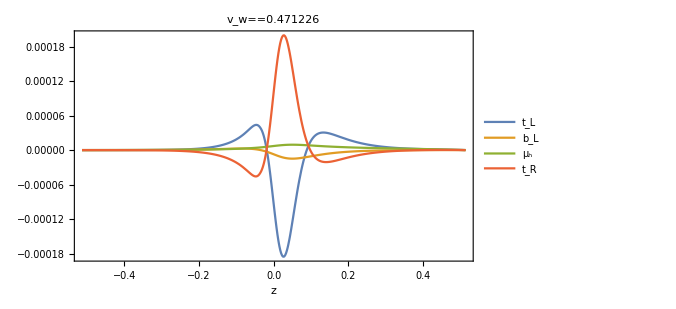
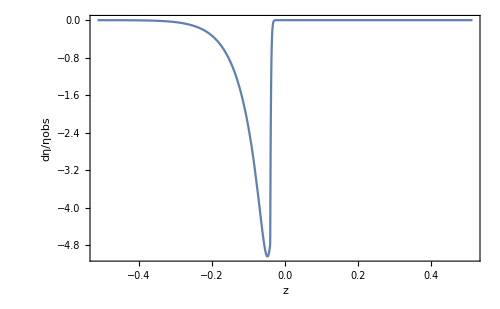
{-Graphics-,-Graphics-,0.35079}

```mathematica
MasterOutputVel[59,588.,400]
```

```mathematica
BAUscale[i_]:=Module[{BAU,res},
BAU[Λ_?NumericQ]:=BAU[Λ?NumericQ]=MasterOutputVel[i,Λ,400][[3]];
If[BAU[100]<1,Return[99]];
Quiet[
res=Λ/.FindRoot[BAU[Λ]-1,{Λ,100,1000},AccuracyGoal->2,PrecisionGoal->2(*,EvaluationMonitor:>Print["Λ=",Λ," BAU=",BAU[Λ]]*)];
];
MasterPars[i];
Print["Λ=",res];
Return[res]
];
```

```mathematica
BAULambda80=ParallelTable[Join[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]]},{BAUscale[i]}],{i,1,Length[Tnlist]}];
Export["SCANS/BAU_1.csv",BAULambda80]
```

Pars α=0.0212568 T =96.1139 v =0.629551 T =108.841 v =0.477451 h =204.114 L =
                  n          w           p          p           0          h
 
>   0.0390251 s =141.399 s =65.1763 L =0.0387468 ds=-0.148164
               l          h          s

Λ=556.619

Pars α=0.0250779 T =92.1907 v =0.648732 T =106.72 v =0.473246 h =207.299 L =
                  n          w           p         p           0          h
 
>   0.0400489 s =141.994 s =67.0877 L =0.0393153 ds=-0.120724
               l          h          s

Λ=567.125

Pars α=0.0221292 T =89.5815 v =0.624734 T =101.159 v =0.474674 h =214.079 L =
                  n          w           p          p           0          h
 
>   0.0428646 s =191.994 s =160.085 L =0.0365933 ds=0.351624
               l          h          s

Λ=104.038

Pars α=0.0214126 T =93.4585 v =0.621225 T =105.116 v =0.475595 h =207.976 L =
                  n          w           p          p           0          h
 
>   0.0412115 s =305.534 s =251.476 L =0.0412115 ds=0.0554918
               l          h          s

Λ=147.386

Pars α=0.022482 T =89.1586 v =0.623879 T =100.66 v =0.473757 h =214.816 L =
                 n          w           p         p           0          h
 
>   0.0430684 s =199.935 s =166.521 L =0.036724 ds=0.366121
               l          h          s

Λ=110.781

Pars α=0.0218778 T =89.8635 v =0.619212 T =100.97 v =0.4742 h =214.192 L =
                  n          w           p         p         0          h
 
>   0.0427348 s =196.225 s =162.076 L =0.0364814 ds=0.349502
               l          h          s

Λ=101.128

Pars α=0.0234285 T =88.3989 v =0.632123 T =100.635 v =0.473313 h =214.797 L =
                  n          w           p          p           0          h
 
>   0.0428079 s =192.343 s =159.376 L =0.036567 ds=0.349799
               l          h          s

Λ=103.188

Pars α=0.0266307 T =89.0636 v =0.651079 T =103.517 v =0.470775 h =210.332 L =
                  n          w           p          p           0          h
 
>   0.0427129 s =319.724 s =261.768 L =0.0427129 ds=0.0235168
               l          h          s

Λ=202.596

Pars α=0.0252194 T =86.7987 v =0.638625 T =99.6068 v =0.470971 h =216.089 L =
                  n          w           p          p           0          h
 
>   0.0437698 s =200.102 s =164.721 L =0.0373533 ds=0.357581
               l          h          s

Λ=115.185

Pars α=0.0256568 T =89.1751 v =0.643326 T =102.813 v =0.471056 h =211.134 L =
                  n          w           p          p           0          h
 
>   0.0431602 s =309.121 s =255.554 L =0.0431602 ds=0.0780253
               l          h          s

Λ=171.834

Pars α=0.0243227 T =87.5643 v =0.635076 T =100.059 v =0.472057 h =215.332 L =
                  n          w           p          p           0          h
 
>   0.0434806 s =195.275 s =161.689 L =0.0371106 ds=0.347484
               l          h          s

Λ=108.603

Pars α=0.0236049 T =88.3124 v =0.631418 T =100.5 v =0.472814 h =215.066 L =
                  n          w           p        p           0          h
 
>   0.0427998 s =194.024 s =159.049 L =0.0365846 ds=0.350157
               l          h          s

Λ=113.894

Pars α=0.0227937 T =88.9102 v =0.626666 T =100.66 v =0.473612 h =214.784 L =
                  n          w           p         p           0          h
 
>   0.0431129 s =196.982 s =163.71 L =0.0367856 ds=0.359553
               l          h         s

Λ=112.968

Pars α=0.0267141 T =88.1821 v =0.648105 T =102.233 v =0.470016 h =211.916 L =
                  n          w           p          p           0          h
 
>   0.0435833 s =296.545 s =243.305 L =0.0435833 ds=0.0874216
               l          h          s

Λ=169.787

Pars α=0.0282073 T =90.3243 v =0.672221 T =107.245 v =0.472343 h =206.506 L =
                  n          w           p          p           0          h
 
>   0.0403401 s =137.448 s =55.2658 L =0.0412774 ds=-0.210751
               l          h          s

Λ=588.883

Pars α=0.0222493 T =89.5513 v =0.623119 T =101.005 v =0.474116 h =214.336 L =
                  n          w           p          p           0          h
 
>   0.0424326 s =193.651 s =159.437 L =0.0362574 ds=0.350123
               l          h          s

Λ=110.045

Pars α=0.0257504 T =86.5105 v =0.64779 T =100.147 v =0.471769 h =215.473 L =
                  n          w          p          p           0          h
 
>   0.0437963 s =188.823 s =155.264 L =0.0374644 ds=0.339868
               l          h          s

Λ=105.264

Pars α=0.0273074 T =85.3931 v =0.654162 T =99.6073 v =0.470159 h =216.048 L =
                  n          w           p          p           0          h
 
>   0.0440684 s =188.397 s =152.87 L =0.0377361 ds=0.328938
               l          h         s

Λ=169.175

Pars α=0.0229948 T =88.6259 v =0.627091 T =100.402 v =0.473266 h =214.955 L =
                  n          w           p          p           0          h
 
>   0.0432318 s =199.242 s =166.815 L =0.0368458 ds=0.361823
               l          h          s

Λ=107.848

Pars α=0.0282617 T =87.0088 v =0.655993 T =101.774 v =0.468819 h =212.495 L =
                  n          w           p          p           0          h
 
>   0.0434984 s =292.478 s =239.724 L =0.0434984 ds=0.0815491
               l          h          s

Λ=191.5

Pars α=0.0214965 T =90.1918 v =0.615745 T =100.992 v =0.474413 h =214.343 L =
                  n          w           p          p           0          h
 
>   0.0426973 s =201.162 s =166.23 L =0.0364238 ds=0.363202
               l          h         s

Λ=112.448

Pars α=0.0223777 T =96.3744 v =0.685836 T =115.13 v =0.485724 h =196.358 L =
                  n          w           p         p           0          h
 
>   0.0398252 s =-36.538 s =30.5939 L =0.0398252 ds=-0.174806
               l          h          s

Λ=403.645

Pars α=0.0273968 T =87.9961 v =0.653047 T =102.552 v =0.469767 h =211.547 L =
                  n          w           p          p           0          h
 
>   0.0433778 s =295.448 s =240.542 L =0.0433778 ds=0.0590276
               l          h          s

Λ=224.894

Pars α=0.0285864 T =84.2568 v =0.660317 T =98.9803 v =0.469155 h =216.866 L =
                  n          w           p          p           0          h
 
>   0.0440778 s =195.053 s =160.405 L =0.0376599 ds=0.348077
               l          h          s

Λ=120.017

Pars α=0.0295801 T =83.2776 v =0.662734 T =98.1573 v =0.467944 h =217.746 L =
                  n          w           p          p           0          h
 
>   0.0445921 s =206.01 s =172.762 L =0.0379678 ds=0.369805
               l         h          s

Λ=120.681

Pars α=0.0274942 T =88.3758 v =0.655382 T =103.223 v =0.470072 h =210.731 L =
                  n          w           p          p           0          h
 
>   0.0429315 s =315.433 s =257.538 L =0.0429315 ds=0.0231626
               l          h          s

Λ=227.268

Pars α=0.0285926 T =84.2591 v =0.661063 T =99.0513 v =0.469302 h =216.869 L =
                  n          w           p          p           0          h
 
>   0.0446082 s =195.387 s =160.614 L =0.0381129 ds=0.350804
               l          h          s

Λ=113.737

Pars α=0.0297072 T =83.5517 v =0.665052 T =98.705 v =0.468226 h =217.137 L =
                  n          w           p         p           0          h
 
>   0.0442072 s =193.859 s =158.039 L =0.0378023 ds=0.339634
               l          h          s

Λ=170.878

Pars α=0.030321 T =83.1794 v =0.672431 T =99.0119 v =0.468798 h =216.762 L =
                 n          w           p          p           0          h
 
>   0.0443241 s =188.269 s =154.124 L =0.0379336 ds=0.331499
               l          h          s

Λ=139.494

Pars α=0.0287706 T =84.2143 v =0.680674 T =100.865 v =0.473185 h =214.407 L =
                  n          w           p          p           0          h
 
>   0.0452701 s =190.759 s =156.456 L =0.0387039 ds=0.341858
               l          h          s

Λ=115.617

Pars α=0.0286865 T =84.2868 v =0.660798 T =99.0705 v =0.469081 h =216.64 L =
                  n          w           p          p           0         h
 
>   0.0439476 s =191.098 s =156.036 L =0.0375919 ds=0.334209
               l          h          s

Λ=158.17

Pars α=0.0237408 T =87.9949 v =0.629754 T =100.016 v =0.472218 h =215.403 L =
                  n          w           p          p           0          h
 
>   0.0433961 s =200.625 s =166.624 L =0.0370004 ds=0.358023
               l          h          s

Λ=105.848

Pars α=0.0245223 T =89.8283 v =0.63622 T =102.775 v =0.471879 h =211.08 L =
                  n          w          p          p           0         h
 
>   0.0431061 s =297.142 s =246.892 L =0.0431061 ds=0.0975165
               l          h          s

Λ=157.169

Pars α=0.028913 T =84.2154 v =0.66522 T =99.4162 v =0.469627 h =216.365 L =
                 n          w          p          p           0          h
 
>   0.0439629 s =186.65 s =151.837 L =0.0475754 ds=0.183671
               l         h          s

Λ=108.353

Pars α=0.0308794 T =85.426 v =0.66974 T =101.49 v =0.467279 h =212.927 L =
                  n         w          p         p           0          h
 
>   0.0442969 s =320.012 s =264.238 L =0.0442969 ds=0.0622059
               l          h          s

Λ=186.132

Pars α=0.0231313 T =88.6643 v =0.628964 T =100.624 v =0.473332 h =214.794 L =
                  n          w           p          p           0          h
 
>   0.0431432 s =194.311 s =160.635 L =0.0368417 ds=0.351907
               l          h          s

Λ=105.425

Pars α=0.0309138 T =83.0308 v =0.682251 T =99.8297 v =0.469992 h =215.389 L =
                  n          w           p          p           0          h
 
>   0.0479696 s =-198.782 s =-163.559 L =0.0479696 ds=0.233212
               l           h           s

Λ=104.97

Pars α=0.0309447 T =88.349 v =0.684287 T =106.431 v =0.470478 h =207.626 L =
                  n         w           p          p           0          h
 
>   0.0399744 s =140.923 s =57.7351 L =0.0409646 ds=-0.209557
               l          h          s

Λ=615.194

Pars α=0.0223969 T =91.8137 v =0.624072 T =103.663 v =0.473976 h =209.903 L =
                  n          w           p          p           0          h
 
>   0.0422351 s =304.924 s =253.526 L =0.0422351 ds=0.105755
               l          h          s

Λ=147.245

Pars α=0.0313961 T =82.6009 v =0.67906 T =99.0587 v =0.468505 h =216.292 L =
                  n          w          p          p           0          h
 
>   0.0501673 s =-213.22 s =-175.737 L =0.0501673 ds=0.247633
               l          h           s

Λ=105.337

Pars α=0.031522 T =87.7355 v =0.685723 T =105.909 v =0.469793 h =208.474 L =
                 n          w           p          p           0          h
 
>   0.0401322 s =134.797 s =55.6674 L =0.0407169 ds=-0.187712
               l          h          s

Λ=598.353

Pars α=0.029857 T =83.148 v =0.663208 T =98.0776 v =0.467572 h =217.813 L =
                 n         w           p          p           0          h
 
>   0.0445629 s =205.059 s =170.772 L =0.0379655 ds=0.364532
               l          h          s

Λ=119.783

Pars α=0.0238456 T =91.1228 v =0.635275 T =104.077 v =0.47306 h =209.438 L =
                  n          w           p          p          0          h
 
>   0.0422317 s =317.147 s =263.09 L =0.0422317 ds=0.0465494
               l          h         s

Λ=166.27

Pars α=0.0303973 T =83.0449 v =0.681892 T =99.7574 v =0.470752 h =215.803 L =
                  n          w           p          p           0          h
 
>   0.0457265 s =195.008 s =159.739 L =0.0390647 ds=0.345804
               l          h          s

Λ=116.844

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars α=0.0334239 T =81.0504 v =0.683748 T =97.8404 v =0.466371 h =218.13 L =
                  n          w           p          p           0         h
 
>   0.0451338 s =197.887 s =163.036 L =0.0385308 ds=0.349729
               l          h          s

Λ=126.065

Pars α=0.0305171 T =85.8863 v =0.668718 T =101.9 v =0.467658 h =212.456 L =
                  n          w           p        p           0          h
 
>   0.0439701 s =297.871 s =240.921 L =0.0439701 ds=0.0461732
               l          h          s

Λ=279.149

Pars α=0.0240306 T =94.993 v =0.686667 T =113.812 v =0.482777 h =198.407 L =
                  n         w           p          p           0          h
 
>   0.0443578 s =-37.4805 s =31.8919 L =0.0443578 ds=-0.194124
               l           h          s

Λ=389.245

Pars α=0.034114 T =80.705 v =0.683306 T =97.4485 v =0.465211 h =218.506 L =
                 n         w           p          p           0          h
 
>   0.0457392 s =201.127 s =164.076 L =0.0468447 ds=0.237613
               l          h          s

Λ=131.485

Pars α=0.0246436 T =87.4888 v =0.645021 T =100.889 v =0.473362 h =214.647 L =
                  n          w           p          p           0          h
 
>   0.0434768 s =184.788 s =152.525 L =0.0372256 ds=0.336461
               l          h          s

Λ=102.732

Pars α=0.0305812 T =85.6761 v =0.668358 T =101.623 v =0.467471 h =212.759 L =
                  n          w           p          p           0          h
 
>   0.0436042 s =281.108 s =226.582 L =0.0436041 ds=0.0552345
               l          h          s

Λ=286.549

Pars α=0.0360443 T =82.0685 v =0.691766 T =100.099 v =0.464324 h =214.674 L =
                  n          w           p          p           0          h
 
>   0.0450304 s =279.072 s =224.741 L =0.0450304 ds=0.0744269
               l          h          s

Λ=297.067

Pars α=0.0368227 T =79.3995 v =0.703885 T =98.093 v =0.46612 h =217.865 L =
                  n          w           p         p          0          h
 
>   0.0458793 s =188.42 s =152.894 L =0.0392934 ds=0.326614
               l         h          s

Λ=180.392

Pars α=0.0291149 T =83.7931 v =0.677308 T =100.074 v =0.47188 h =215.269 L =
                  n          w           p          p          0          h
 
>   0.0457877 s =199.947 s =165.313 L =0.039048 ds=0.355164
               l          h          s

Λ=105.789

Pars α=0.0306 T =82.9516 v =0.670346 T =98.5768 v =0.467876 h =217.36 L =
               n          w           p          p           0         h
 
>   0.0444247 s =193.805 s =157.955 L =0.0379921 ds=0.341888
               l          h          s

Λ=170.752

Pars α=0.0318494 T =83.7419 v =0.697186 T =102.275 v =0.471861 h =212.459 L =
                  n          w           p          p           0          h
 
>   0.0450978 s =-188.849 s =-155.647 L =0.0450978 ds=0.0985829
               l           h           s

Λ=105.286

Pars α=0.0342666 T =80.8659 v =0.697136 T =98.992 v =0.468198 h =216.387 L =
                  n          w           p         p           0          h
 
>   0.0493045 s =-202.718 s =-166.97 L =0.0493045 ds=0.242795
               l           h          s

Λ=105.905

Pars α=0.0368347 T =82.5989 v =0.699083 T =101.555 v =0.464946 h =212.962 L =
                  n          w           p          p           0          h
 
>   0.0439753 s =322.365 s =261.505 L =0.0439753 ds=0.00312772
               l          h          s

Λ=319.286

Pars α=0.0376853 T =78.6934 v =0.704044 T =97.3114 v =0.464956 h =218.801 L =
                  n          w           p          p           0          h
 
>   0.0363071 s =199.019 s =164.555 L =0.0310557 ds=0.353363
               l          h          s

Λ=266.572

Pars α=0.0325384 T =83.3091 v =0.699691 T =102.074 v =0.471379 h =212.683 L =
                  n          w           p          p           0          h
 
>   0.0452754 s =-185.709 s =-151.797 L =0.0452753 ds=0.100151
               l           h           s

Λ=106.598

Pars α=0.0348282 T =83.442 v =0.689128 T =101.395 v =0.465491 h =213.127 L =
                  n         w           p          p           0          h
 
>   0.0439482 s =309.134 s =250.486 L =0.0439482 ds=0.0236225
               l          h          s

Λ=307.537

Pars α=0.0383116 T =78.6844 v =0.710641 T =98.016 v =0.465727 h =217.427 L =
                  n          w           p         p           0          h
 
>   0.0505891 s =-214.709 s =-176.87 L =0.0505891 ds=0.243282
               l           h          s

Λ=115.06

Pars α=0.0318679 T =82.0942 v =0.678606 T =98.4565 v =0.467646 h =217.535 L =
                  n          w           p          p           0          h
 
>   0.0453255 s =194.244 s =159.249 L =0.0387424 ds=0.345341
               l          h          s

Λ=126.24

Pars α=0.0368652 T =79.4439 v =0.709858 T =98.7575 v =0.467517 h =216.649 L =
                  n          w           p          p           0          h
 
>   0.0499166 s =-202.371 s =-166.775 L =0.0499166 ds=0.240865
               l           h           s

Λ=104.748

Pars α=0.0379191 T =78.6464 v =0.700895 T =96.9655 v =0.463865 h =219.146 L =
                  n          w           p          p           0          h
 
>   0.0360723 s =200.745 s =163.753 L =0.0308797 ds=0.348512
               l          h          s

Λ=316.83

Pars α=0.0394627 T =77.9212 v =0.70838 T =96.9337 v =0.463612 h =219.06 L =
                  n          w          p          p           0         h
 
>   0.0362229 s =196.813 s =160.554 L =0.0310272 ds=0.338734
               l          h          s

Λ=311.583

Pars α=0.0326811 T =81.5607 v =0.684156 T =98.4221 v =0.467616 h =217.592 L =
                  n          w           p          p           0          h
 
>   0.044995 s =194.028 s =159.988 L =0.0384532 ds=0.347302
              l          h          s

Λ=113.943

Pars α=0.0350178 T =80.1789 v =0.697885 T =98.2949 v =0.467269 h =217.621 L =
                  n          w           p          p           0          h
 
>   0.046003 s =192.384 s =159.762 L =0.0392995 ds=0.342462
              l          h          s

Λ=115.295

Pars α=0.0369522 T =79.3104 v =0.699455 T =97.5581 v =0.464868 h =218.484 L =
                  n          w           p          p           0          h
 
>   0.045491 s =193.834 s =156.356 L =0.0469895 ds=0.220623
              l          h          s

Λ=177.109

Pars α=0.0383279 T =81.7063 v =0.703921 T =101.082 v =0.464042 h =213.39 L =
                  n          w           p          p           0         h
 
>   0.0347805 s =298.634 s =239.667 L =0.0347805 ds=0.00711937
               l          h          s

Λ=496.343

Pars α=0.0381273 T =78.5929 v =0.706247 T =97.4434 v =0.464889 h =218.597 L =
                  n          w           p          p           0          h
 
>   0.0360861 s =193.901 s =158.705 L =0.0309235 ds=0.340117
               l          h          s

Λ=291.974

Pars α=0.0402435 T =80.3302 v =0.709684 T =100.13 v =0.462905 h =214.541 L =
                  n          w           p         p           0          h
 
>   0.0357052 s =329.776 s =271.325 L =0.0357052 ds=0.0461344
               l          h          s

Λ=450.678

Pars α=0.035128 T =85.7552 v =0.703483 T =105.714 v =0.468786 h =208.434 L =
                 n          w           p          p           0          h
 
>   0.0405404 s =138.263 s =55.2961 L =0.0417073 ds=-0.218568
               l          h          s

Λ=615.346

Pars α=0.0328583 T =81.5681 v =0.686795 T =98.7014 v =0.467942 h =216.563 L =
                  n          w           p          p           0          h
 
>   0.04898 s =-213.32 s =-178. L =0.0489799 ds=0.248139
             l          h        s

Λ=101.11

Pars α=0.0370065 T =79.261 v =0.705027 T =98.0521 v =0.46614 h =217.907 L =
                  n         w           p          p          0          h
 
>   0.0360235 s =188.392 s =154.012 L =0.0309153 ds=0.329894
               l          h          s

Λ=280.972

Pars α=0.0385381 T =78.3831 v =0.703526 T =96.9498 v =0.463657 h =219.133 L =
                  n          w           p          p           0          h
 
>   0.0361028 s =198.973 s =161.708 L =0.0309262 ds=0.343033
               l          h          s

Λ=324.792

Pars α=0.0330783 T =86.7156 v =0.692364 T =105.529 v =0.468881 h =209.004 L =
                  n          w           p          p           0          h
 
>   0.0403956 s =138.418 s =58.2284 L =0.0408453 ds=-0.180765
               l          h          s

Λ=611.938

Pars α=0.0404398 T =77.4237 v =0.713273 T =96.8839 v =0.463557 h =219.211 L =
                  n          w           p          p           0          h
 
>   0.036556 s =198.028 s =162.089 L =0.031297 ds=0.345047
              l          h          s

Λ=300.286

Pars α=0.0355775 T =80.033 v =0.700252 T =98.4007 v =0.467018 h =216.971 L =
                  n         w           p          p           0          h
 
>   0.0497787 s =-208.759 s =-172.891 L =0.0497787 ds=0.247446
               l           h           s

Λ=105.041

Pars α=0.038823 T =78.4066 v =0.707348 T =97.3809 v =0.464214 h =218.644 L =
                 n          w           p          p           0          h
 
>   0.0361731 s =191.284 s =153.885 L =0.0310641 ds=0.326432
               l          h          s

Λ=332.611

Pars α=0.036406 T =79.2113 v =0.696538 T =97.1048 v =0.464944 h =218.995 L =
                 n          w           p          p           0          h
 
>   0.0465054 s =205.827 s =171.53 L =0.0396151 ds=0.365633
               l          h         s

Λ=124.807

Pars α=0.0391536 T =81.0942 v =0.706268 T =100.636 v =0.463499 h =213.952 L =
                  n          w           p          p           0          h
 
>   0.0351656 s =319.481 s =259.734 L =0.0351656 ds=0.0286318
               l          h          s

Λ=485.352

Pars α=0.0409847 T =80.3728 v =0.713756 T =100.67 v =0.462971 h =213.91 L =
                  n          w           p         p           0         h
 
>   0.0350195 s =305.9 s =246.198 L =0.0350195 ds=0.0109197
               l        h          s

Λ=504.407

Pars α=0.0426299 T =79.4135 v =0.718889 T =100.139 v =0.462201 h =214.551 L =
                  n          w           p          p           0          h
 
>   0.0356318 s =309.353 s =250.468 L =0.0356318 ds=0.0266802
               l          h          s

Λ=488.263

SCANS/BAU_1.csv

## Find viable parameter space

```mathematica
(*ClearAll["Global`*"];*)
SetDirectory[NotebookDirectory[]];
SetOptions[{ParametricPlot,ListLinePlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot,ListContourPlot,LogPlot,Plot,RegionPlot,ContourPlot},Frame->True,BaseStyle->{FontColor->Black,FontWeight->"Normal",FontSize->16,FontFamily->"Times"},Axes->False,PlotLegends->Automatic,AspectRatio->1,ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->Full];
colours=ColorData[97,"ColorList"];
WP=MachinePrecision;
(*******************************************************************************************************************)
(**********************************************************************************************)
```

```mathematica
(*gtab=Import["standardmodel2018.txt","Table",HeaderLines->8][[;;;;20]];*)
gtab=Import["./satoshi_dof.dat","Table",HeaderLines->8][[;;;;20]];
gstar[T_]:=Interpolation[gtab[[All,{1,2}]]][T];
gsstar[T_]:=Interpolation[gtab[[All,{1,4}]]][T];
(*****************************************************************************************************)
(*****************************************************************************************************)
```

```mathematica
params3=Import["SCANS/to_test_BAU.csv","Dataset","HeaderLines"->1];
```

```mathematica
Tnlist=params3[All,"Tnuc_0"];
TpoverTnlist=params3[All,"Tp/TN"];
vwlist=params3[All,"vw"];
vplist=params3[All,"vp"];
h0list=params3[All,"h0"];
Lhlist=params3[All,"Lh"];
Lslist=params3[All,"Ls"];
dslist=params3[All,"ds"];
shighlist=params3[All,"shigh"];
slowlist=params3[All,"slow"];
alphalist=params3[All,"alpha_max"];
(*alphalist=params3[All,"alpha"];
betalist=params3[All,"d/dT(S_3/T)"];*)
```

```mathematica
MasterFunction[Tn_,vw_,h0_,Lh_,sl_,sh_,Ls_,ds_,ΛCP_,Infty_,points_]:=MasterFunction[Tn,vw,h0,Lh,sl,sh,Ls,ds,ΛCP,Infty,points]=Module[{ηobs=8 10^-11,β=1/Tn,Γsph=10^-6 Tn,h,s,mt,Bond,Equation,sol,μtlsol,μtrsol,μblsol,μhsol,μBL,fsph,gdof,ηB,Plot1,Plot2,
ΓSS=4.9*10^-4 Tn,
Γy=4.2*10^-3 Tn,Dq=6/Tn(*quark diffusion constant*),
Dh=20/Tn(*higgs diffusion constant*),
inf=Infty Lh (*defines the region of interpolation/integration*)},
pw=√(w^2-x^2);(*Formula defined after A3*)
pz=1/(√(1-vw^2))(y pw-w vw);(*Formula defined after A3*)
Eb=1/(√(1-vw^2))(w-vw y pw);(*Formula defined after A3*)
Vs = √(pz^2)/√(pz^2+x^2);(*Formula  A4*)
Vh=Vs^2 1/(√(1-x^2/Eb^2));(*Formula  A5*);
ff=1/(Exp[β w]+1);(*Distribution funcion for fermion *)
fb=1/(Exp[β w]-1);(*Distribution funcion for boson *)
ff1=D[ff,w];(*Derivative of Distribution funcion for fermion *)
fb1=D[fb,w];(*Derivative of Distribution funcion for boson *)
ff2=D[ff1,w];(*Second Derivative of Distribution funcion for fermion *)
fb2=D[fb1,w];(*Second Derivative of Distribution funcion for boson *)
h[z_]:=h0/2(Tanh[z/Lh]+1);(**equation (50) LEFT MOVING WALL!!**)
(*s[z_]:=s0/2(1-Tanh[z/Ls-ds]);*)(**equation (50)**)
s[z_]:=(sl-sh)/2 Tanh[z/Ls-ds]+(sl+sh)/2;
mt[z_]:=0.99571/(√2) h[z] √(1+s[z]^2/ΛCP^2);(**equation (49)**)
θ[z_]:=ArcTan[s[z]/ΛCP];(**equation (49)**)
mb[z_]:=4.2*h[z]/h0 ;
mh[z_]:=125.3*h[z]/h0 ;
Γm[z_]:=mt[z]^2/(63 Tn);
mW[z_]:=0.65 h[z]/2 (*W boson mass*);
Γh[z_]:=mW[z]^2/(50Tn);
Xmax=Max[{mt[inf],mh[inf],mb[inf],mW[inf]}]+0.1(*Max value of x used for interpolating coefficient functions*);Kf0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2 NIntegrate[pw Eb ff/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for fermions*);
Kb0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for bosons*);
Kf0inter=Interpolation[Table[{x,Kf0[x,vw]},{x,0,Xmax,Xmax/10}]];
Kb0inter=Interpolation[Table[{x,Kb0[x,vw]},{x,0,Xmax,Xmax/10}]];
K0t[z_]:=Kf0inter[mt[z]];
K0b[z_]:=Kf0inter[mb[z]];
K0h[z_]:=Kb0inter[mh[z]];Df0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=0*);
Db0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=0*);Df0inter=Interpolation[Table[{x,Df0[x,vw]},{x,0,Xmax,Xmax/10}]];
Db0inter=Interpolation[Table[{x,Db0[x,vw]},{x,0,Xmax,Xmax/10}]];
D0t[z_]:=Df0inter[mt[z]];
D0b[z_]:=Df0inter[mb[z]];
D0h[z_]:=Db0inter[mh[z]];Df1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=1*);
Db1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=1*);
Df1inter=Interpolation[Table[{x,Df1[x,vw]},{x,0,Xmax,Xmax/10}]];
Db1inter=Interpolation[Table[{x,Db1[x,vw]},{x,0,Xmax,Xmax/10}]];
D1t[z_]:=Df1inter[mt[z]];
D1b[z_]:=Df1inter[mb[z]];
D1h[z_]:=Db1inter[mh[z]];Df2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=2*);
Db2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=2*);Df2inter=Interpolation[Table[{x,Df2[x,vw]},{x,0,Xmax,Xmax/10}]];
Db2inter=Interpolation[Table[{x,Db2[x,vw]},{x,0,Xmax,Xmax/10}]];
D2t[z_]:=Df2inter[mt[z]];
D2b[z_]:=Df2inter[mb[z]];
D2h[z_]:=Db2inter[mh[z]];Qf1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[pw  ff2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞}](*Formula (27) for fermions, l=1*);
Qb1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[pw  fb2/.{x->0,vvw->vi},{y,-1,1}],{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw  fb2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞},WorkingPrecision->10]](*Formula (27) for bosons, l=1*);
Qf1inter=Interpolation[Table[{x,Qf1[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb1inter=Interpolation[Table[{x,Qb1[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1t[z_]:=Qf1inter[mt[z]];
Q1b[z_]:=Qf1inter[mb[z]];
Q1h[z_]:=Qb1inter[mh[z]];
Qf2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[(pw pz)/Eb ff2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10](*Formula (27) for fermions, l=2*);
Qb2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{y,-1,1}],{w,xi,∞,xi},Method->PrincipalValue],NIntegrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (27) for bosons, l=2*);Qf2inter=Interpolation[Table[{x,Qf2[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb2inter=Interpolation[Table[{x,Qb2[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2t[z_]:=Qf2inter[mt[z]];
Q2b[z_]:=Qf2inter[mb[z]];
Q2h[z_]:=Qb2inter[mh[z]];
Q1fo8integrand=FullSimplify[(Integrate[pw/pz Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh ff1/.{x->0,vw->vi},y]/.{y->-1})];Q1bo8integrand=FullSimplify[(Integrate[pw/pz Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh fb1/.{x->0,vw->vi},y]/.{y->-1})];Q1fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=1, helicity eigenstates*);
Q1bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=1, helicity eigenstates*);Q1fo8inter=Interpolation[Table[{x,Q1fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1bo8inter=Interpolation[Table[{x,Q1bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o8t[z_]:=Q1fo8inter[mt[z]];
Q1o8b[z_]:=Q1fo8inter[mb[z]];
Q1o8h[z_]:=Q1bo8inter[mh[z]];Q2fo8integrand=FullSimplify[(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->-1})];Q2bo8integrand=FullSimplify[(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=2, helicity eigenstates*);
Q2bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=2, helicity eigenstates*);Q2fo8inter=Interpolation[Table[{x,Q2fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2bo8inter=Interpolation[Table[{x,Q2bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2o8t[z_]:=Q2fo8inter[mt[z]];
Q2o8b[z_]:=Q2fo8inter[mb[z]];
Q2o8h[z_]:=Q2bo8inter[mh[z]];
Q1fo9integrand=FullSimplify[(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q1fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q1fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (41), l=1, helicity eigenstates*);Q1fo9nter=Interpolation[Table[{x,Q1fo9[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o9t[z_]:=Q1fo9nter[mt[z]];
Q1o9b[z_]:=Q1fo9nter[mb[z]];
Q2fo9integrand=FullSimplify[(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q2fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->15]](*Formula (41) for fermions, l=2, helicity eigenstates*);Q2fo9inter=Interpolation[Table[{x,Q2fo9[x,vw]},{x,0,Xmax,Xmax/10}]];Q2o9t[z_]:=Q2fo9inter[mt[z]];
Q2o9b[z_]:=Q2fo9inter[mb[z]];
St1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q1o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q1o9t[z])/.{z->zz}];Sb1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q1o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q1o9b[z])/.{z->zz}];St2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q2o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q2o9t[z])/.{z->zz}];Sb2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q2o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q2o9b[z])/.{z->zz}];
Γhtot[z_]:=D2h[z]/(Dh D0h[z])(*W scattering rate. This was not provided in the paper and we took it directly from ref [47] 0605242*);Γttot[z_]:=D2t[z]/(Dq D0t[z]);
Γbtot[z_]:=D2b[z]/(Dq D0b[z]);
δCtL1[z_]:=β K0t[z] (Γy(μtl[z]-μtr[z]+μh[z])+Γm[z](μtl[z]-μtr[z])+Γhtot[z](μtl[z]-μbl[z])+ ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]))(*Formula (53), we divide by T to get dimensions right*);δCtL2[z_]:=(-Γttot[z]utl[z]-vw δCtL1[z]);
δCbL1[z_]:=β K0b[z](Γy(μbl[z]-μtr[z]+μh[z])+Γhtot[z](μbl[z]-μtl[z])+ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));δCbL2[z_]:=(-Γbtot[z]ubl[z]-vw δCbL1[z]);δCtR1[z_]:=β K0t[z](-Γy(μtl[z]+μbl[z]-2μtr[z]+2μh[z])-Γm[z](μtl[z]-μtr[z])-ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));
δCtR2[z_]:=(-Γttot[z]utr[z]-vw δCtR1[z]);
δCh1[z_]:=β K0h[z]( Γy (μtl[z]+μbl[z]-2μtr[z]+2μh[z])+Γh[z] μh[z]);
δCh2[z_]:=(-Γhtot[z]uh[z]-vw δCh1[z]);
{htl,htr,hbl}={-1,1,-1};TopLeft1={-D1t[z] μtl'[z]+utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q1t[z] μtl[z]-δCtL1[z]==htl St1[z]};TopLeft2={-D2t[z] μtl'[z]-vw utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtl[z]-δCtL2[z]== htl St2[z]};
BottomLeft1={-D1b[z] μbl'[z]+ubl'[z]+ D[(mb[z])^2,z] vw/(√(1-vw^2))Q1b[z] μbl[z]-δCbL1[z]==hbl Sb1[z]};BottomLeft2={-D2b[z] μbl'[z]-vw ubl'[z]+D[(mb[z])^2,z] vw/(√(1-vw^2)) Q2b[z] μbl[z]-δCbL2[z]==hbl Sb2[z]};TopRight1={-D1t[z] μtr'[z]+utr'[z]+ D[(mt[z])^2,z] vw/(√(1-vw^2))Q1t[z] μtr[z]-δCtR1[z]==htr St1[z]};TopRight2={-D2t[z] μtr'[z]-vw utr'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtr[z]-δCtR2[z]==htr St2[z]};Higgs1={-D1h[z] μh'[z]+uh'[z]+ D[(mh[z])^2,z] vw/(√(1-vw^2))Q1h[z] μh[z]-δCh1[z]==0};
Higgs2={-D2h[z] μh'[z]-vw uh'[z]+D[(mh[z])^2,z] vw/(√(1-vw^2)) Q2h[z] μh[z]-δCh2[z]==0};
Bond={ μtl[inf]==0,μtr[inf]==0,μbl[inf]==0,μh[inf]==0, μtl[-inf]==0,μtr[-inf]==0,μbl[-inf]==0,μh[-inf]==0};Equation=Join[TopLeft1,TopLeft2,TopRight1,TopRight2,BottomLeft1,BottomLeft2,Higgs1,Higgs2,Bond];sol=NDSolve[Equation,{μtl,μtr,μbl,μh, utl,utr,ubl,uh},{z,-inf,inf},Method->{"Shooting",Method->{"FixedStep",Method->"ExplicitEuler"}},StartingStepSize->2inf/points(*,Method->{"Shooting",Method->"StiffnessSwitching"},MaxStepSize->0.01*)];μtlsol[z_]:=μtl[z]/.sol[[1]][[1]];μtrsol[z_]:=μtr[z]/.sol[[1]][[2]];μblsol[z_]:=μbl[z]/.sol[[1]][[3]];μhsol[z_]:=μh[z]/.sol[[1]][[4]];μBL[z_]:=1/2(1+4D0t[z])μtlsol[z]+1/2(1+4D0b[z])μblsol[z]+2 D0t[z] μtrsol[z];
fsph[z_]:=Min[{1,2.5 Tn/Γsph Exp[-40 h[z]/Tn]}];
gdof=gstar[Tn](*106.75*);
ηB=405 Γsph/(4π^2 vw gdof Tn)√(1-vw^2) NIntegrate[μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[vw])(*√(1-vw^2)*)],{z,-inf,inf},Method->"QuasiMonteCarlo",AccuracyGoal->2,PrecisionGoal->2];
Plot2=Plot[405 Γsph/(4π^2 vw gdof Tn)√(1-vw^2)μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[vw])(*√(1-vw^2)*)]/ηobs,{z,-inf,inf},FrameLabel->{"z","dη/ηobs"},PlotRange->All];
Plot1=Plot[{μtlsol[z] β,μblsol[z] β,μhsol[z] β,μtrsol[z]β},{z,-inf,inf},PlotRange->Full,PlotLegends->{"t_L"," b_L"," μ_h","t_R"},PlotLabel->Subscript[v, w]==-vw,FrameLabel->{"z",""},PlotRange->All];
(*Return[Abs[ηB/ηobs]];*)
Return[{Plot1,Plot2,Abs[ηB/ηobs]}];
];
```

```mathematica
(*MasterOutputOld[i_,Λcutoff_,Infty_,points_]:=MasterFunction[Tnlist[[i]],-vwlist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],,shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,Infty,points];*)
```

```mathematica
MasterPars[i_]:=Print[ "Pars α=",alphalist[[i]],(*" β/H=",betalist[[i]],*)" T_n=",Tnlist[[i]]," v_w=",vwlist[[i]]," T_p=",Tnlist[[i]]*TpoverTnlist[[i]]," v_p=",vplist[[i]]," h_0=",h0list[[i]]," L_h=",Lhlist[[i]]," s_l=",slowlist[[i]]," s_h=",shighlist[[i]]," L_s=",Lslist[[i]]," ds=",dslist[[i]]];
```

```mathematica
MasterPars[59]
```

Pars α=0.0275794 T_n=85.2032 v_w=0.661677 T_p=100.1 v_p=0.471226 h_0=214.923 L_h=0.0513349 s_l=-208.571 s_h=-173.732 L_s=0.0513349 ds=0.244537

```mathematica
(*MasterOutput[i_,Λcutoff_,Infty_,points_]:=MasterFunction[Tnlist[[i]]*TpoverTnlist[[i]],-vplist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,Infty,points];*)
```

```mathematica
(*MasterOutputVelOld[i_,Λcutoff_,points_]:=MasterFunction[Tnlist[[i]],-vwlist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],,shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,10,points];*)
MasterOutputVel[i_,Λcutoff_,points_]:=MasterFunction[Tnlist[[i]]*TpoverTnlist[[i]],-vplist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,10,points];
```

```mathematica
params3[58]
```

```mathematica
MasterOutputVel[59,588.,400]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{-Graphics-,-Graphics-,0.35079}

```mathematica
BAUscale[i_]:=Module[{BAU,res},
BAU[Λ_?NumericQ]:=BAU[Λ?NumericQ]=MasterOutputVel[i,Λ,400][[3]];
If[BAU[100]<1,Return[99]];
Quiet[
res=Λ/.FindRoot[BAU[Λ]-1,{Λ,100,1000},AccuracyGoal->2,PrecisionGoal->2(*,EvaluationMonitor:>Print["Λ=",Λ," BAU=",BAU[Λ]]*)];
];
MasterPars[i];
Print["Λ=",res];
Return[res]
];
```

```mathematica
BAULambda80=ParallelTable[Join[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]]},{BAUscale[i]}],{i,1,Length[Tnlist]}];
Export["SCANS/BAU_1.csv",BAULambda80]
```

Pars α=0.0212568 T =96.1139 v =0.629551 T =108.841 v =0.477451 h =204.114 L =
                  n          w           p          p           0          h
 
>   0.0390251 s =141.399 s =65.1763 L =0.0387468 ds=-0.148164
               l          h          s

Λ=556.619

Pars α=0.0250779 T =92.1907 v =0.648732 T =106.72 v =0.473246 h =207.299 L =
                  n          w           p         p           0          h
 
>   0.0400489 s =141.994 s =67.0877 L =0.0393153 ds=-0.120724
               l          h          s

Λ=567.125

Pars α=0.0221292 T =89.5815 v =0.624734 T =101.159 v =0.474674 h =214.079 L =
                  n          w           p          p           0          h
 
>   0.0428646 s =191.994 s =160.085 L =0.0365933 ds=0.351624
               l          h          s

Λ=104.038

Pars α=0.0214126 T =93.4585 v =0.621225 T =105.116 v =0.475595 h =207.976 L =
                  n          w           p          p           0          h
 
>   0.0412115 s =305.534 s =251.476 L =0.0412115 ds=0.0554918
               l          h          s

Λ=147.386

Pars α=0.022482 T =89.1586 v =0.623879 T =100.66 v =0.473757 h =214.816 L =
                 n          w           p         p           0          h
 
>   0.0430684 s =199.935 s =166.521 L =0.036724 ds=0.366121
               l          h          s

Λ=110.781

Pars α=0.0218778 T =89.8635 v =0.619212 T =100.97 v =0.4742 h =214.192 L =
                  n          w           p         p         0          h
 
>   0.0427348 s =196.225 s =162.076 L =0.0364814 ds=0.349502
               l          h          s

Λ=101.128

Pars α=0.0234285 T =88.3989 v =0.632123 T =100.635 v =0.473313 h =214.797 L =
                  n          w           p          p           0          h
 
>   0.0428079 s =192.343 s =159.376 L =0.036567 ds=0.349799
               l          h          s

Λ=103.188

Pars α=0.0266307 T =89.0636 v =0.651079 T =103.517 v =0.470775 h =210.332 L =
                  n          w           p          p           0          h
 
>   0.0427129 s =319.724 s =261.768 L =0.0427129 ds=0.0235168
               l          h          s

Λ=202.596

Pars α=0.0252194 T =86.7987 v =0.638625 T =99.6068 v =0.470971 h =216.089 L =
                  n          w           p          p           0          h
 
>   0.0437698 s =200.102 s =164.721 L =0.0373533 ds=0.357581
               l          h          s

Λ=115.185

Pars α=0.0256568 T =89.1751 v =0.643326 T =102.813 v =0.471056 h =211.134 L =
                  n          w           p          p           0          h
 
>   0.0431602 s =309.121 s =255.554 L =0.0431602 ds=0.0780253
               l          h          s

Λ=171.834

Pars α=0.0243227 T =87.5643 v =0.635076 T =100.059 v =0.472057 h =215.332 L =
                  n          w           p          p           0          h
 
>   0.0434806 s =195.275 s =161.689 L =0.0371106 ds=0.347484
               l          h          s

Λ=108.603

Pars α=0.0236049 T =88.3124 v =0.631418 T =100.5 v =0.472814 h =215.066 L =
                  n          w           p        p           0          h
 
>   0.0427998 s =194.024 s =159.049 L =0.0365846 ds=0.350157
               l          h          s

Λ=113.894

Pars α=0.0227937 T =88.9102 v =0.626666 T =100.66 v =0.473612 h =214.784 L =
                  n          w           p         p           0          h
 
>   0.0431129 s =196.982 s =163.71 L =0.0367856 ds=0.359553
               l          h         s

Λ=112.968

Pars α=0.0267141 T =88.1821 v =0.648105 T =102.233 v =0.470016 h =211.916 L =
                  n          w           p          p           0          h
 
>   0.0435833 s =296.545 s =243.305 L =0.0435833 ds=0.0874216
               l          h          s

Λ=169.787

Pars α=0.0282073 T =90.3243 v =0.672221 T =107.245 v =0.472343 h =206.506 L =
                  n          w           p          p           0          h
 
>   0.0403401 s =137.448 s =55.2658 L =0.0412774 ds=-0.210751
               l          h          s

Λ=588.883

Pars α=0.0222493 T =89.5513 v =0.623119 T =101.005 v =0.474116 h =214.336 L =
                  n          w           p          p           0          h
 
>   0.0424326 s =193.651 s =159.437 L =0.0362574 ds=0.350123
               l          h          s

Λ=110.045

Pars α=0.0257504 T =86.5105 v =0.64779 T =100.147 v =0.471769 h =215.473 L =
                  n          w          p          p           0          h
 
>   0.0437963 s =188.823 s =155.264 L =0.0374644 ds=0.339868
               l          h          s

Λ=105.264

Pars α=0.0273074 T =85.3931 v =0.654162 T =99.6073 v =0.470159 h =216.048 L =
                  n          w           p          p           0          h
 
>   0.0440684 s =188.397 s =152.87 L =0.0377361 ds=0.328938
               l          h         s

Λ=169.175

Pars α=0.0229948 T =88.6259 v =0.627091 T =100.402 v =0.473266 h =214.955 L =
                  n          w           p          p           0          h
 
>   0.0432318 s =199.242 s =166.815 L =0.0368458 ds=0.361823
               l          h          s

Λ=107.848

Pars α=0.0282617 T =87.0088 v =0.655993 T =101.774 v =0.468819 h =212.495 L =
                  n          w           p          p           0          h
 
>   0.0434984 s =292.478 s =239.724 L =0.0434984 ds=0.0815491
               l          h          s

Λ=191.5

Pars α=0.0214965 T =90.1918 v =0.615745 T =100.992 v =0.474413 h =214.343 L =
                  n          w           p          p           0          h
 
>   0.0426973 s =201.162 s =166.23 L =0.0364238 ds=0.363202
               l          h         s

Λ=112.448

Pars α=0.0223777 T =96.3744 v =0.685836 T =115.13 v =0.485724 h =196.358 L =
                  n          w           p         p           0          h
 
>   0.0398252 s =-36.538 s =30.5939 L =0.0398252 ds=-0.174806
               l          h          s

Λ=403.645

Pars α=0.0273968 T =87.9961 v =0.653047 T =102.552 v =0.469767 h =211.547 L =
                  n          w           p          p           0          h
 
>   0.0433778 s =295.448 s =240.542 L =0.0433778 ds=0.0590276
               l          h          s

Λ=224.894

Pars α=0.0285864 T =84.2568 v =0.660317 T =98.9803 v =0.469155 h =216.866 L =
                  n          w           p          p           0          h
 
>   0.0440778 s =195.053 s =160.405 L =0.0376599 ds=0.348077
               l          h          s

Λ=120.017

Pars α=0.0295801 T =83.2776 v =0.662734 T =98.1573 v =0.467944 h =217.746 L =
                  n          w           p          p           0          h
 
>   0.0445921 s =206.01 s =172.762 L =0.0379678 ds=0.369805
               l         h          s

Λ=120.681

Pars α=0.0274942 T =88.3758 v =0.655382 T =103.223 v =0.470072 h =210.731 L =
                  n          w           p          p           0          h
 
>   0.0429315 s =315.433 s =257.538 L =0.0429315 ds=0.0231626
               l          h          s

Λ=227.268

Pars α=0.0285926 T =84.2591 v =0.661063 T =99.0513 v =0.469302 h =216.869 L =
                  n          w           p          p           0          h
 
>   0.0446082 s =195.387 s =160.614 L =0.0381129 ds=0.350804
               l          h          s

Λ=113.737

Pars α=0.0297072 T =83.5517 v =0.665052 T =98.705 v =0.468226 h =217.137 L =
                  n          w           p         p           0          h
 
>   0.0442072 s =193.859 s =158.039 L =0.0378023 ds=0.339634
               l          h          s

Λ=170.878

Pars α=0.030321 T =83.1794 v =0.672431 T =99.0119 v =0.468798 h =216.762 L =
                 n          w           p          p           0          h
 
>   0.0443241 s =188.269 s =154.124 L =0.0379336 ds=0.331499
               l          h          s

Λ=139.494

Pars α=0.0287706 T =84.2143 v =0.680674 T =100.865 v =0.473185 h =214.407 L =
                  n          w           p          p           0          h
 
>   0.0452701 s =190.759 s =156.456 L =0.0387039 ds=0.341858
               l          h          s

Λ=115.617

Pars α=0.0286865 T =84.2868 v =0.660798 T =99.0705 v =0.469081 h =216.64 L =
                  n          w           p          p           0         h
 
>   0.0439476 s =191.098 s =156.036 L =0.0375919 ds=0.334209
               l          h          s

Λ=158.17

Pars α=0.0237408 T =87.9949 v =0.629754 T =100.016 v =0.472218 h =215.403 L =
                  n          w           p          p           0          h
 
>   0.0433961 s =200.625 s =166.624 L =0.0370004 ds=0.358023
               l          h          s

Λ=105.848

Pars α=0.0245223 T =89.8283 v =0.63622 T =102.775 v =0.471879 h =211.08 L =
                  n          w          p          p           0         h
 
>   0.0431061 s =297.142 s =246.892 L =0.0431061 ds=0.0975165
               l          h          s

Λ=157.169

Pars α=0.028913 T =84.2154 v =0.66522 T =99.4162 v =0.469627 h =216.365 L =
                 n          w          p          p           0          h
 
>   0.0439629 s =186.65 s =151.837 L =0.0475754 ds=0.183671
               l         h          s

Λ=108.353

Pars α=0.0308794 T =85.426 v =0.66974 T =101.49 v =0.467279 h =212.927 L =
                  n         w          p         p           0          h
 
>   0.0442969 s =320.012 s =264.238 L =0.0442969 ds=0.0622059
               l          h          s

Λ=186.132

Pars α=0.0231313 T =88.6643 v =0.628964 T =100.624 v =0.473332 h =214.794 L =
                  n          w           p          p           0          h
 
>   0.0431432 s =194.311 s =160.635 L =0.0368417 ds=0.351907
               l          h          s

Λ=105.425

Pars α=0.0309138 T =83.0308 v =0.682251 T =99.8297 v =0.469992 h =215.389 L =
                  n          w           p          p           0          h
 
>   0.0479696 s =-198.782 s =-163.559 L =0.0479696 ds=0.233212
               l           h           s

Λ=104.97

Pars α=0.0309447 T =88.349 v =0.684287 T =106.431 v =0.470478 h =207.626 L =
                  n         w           p          p           0          h
 
>   0.0399744 s =140.923 s =57.7351 L =0.0409646 ds=-0.209557
               l          h          s

Λ=615.194

Pars α=0.0223969 T =91.8137 v =0.624072 T =103.663 v =0.473976 h =209.903 L =
                  n          w           p          p           0          h
 
>   0.0422351 s =304.924 s =253.526 L =0.0422351 ds=0.105755
               l          h          s

Λ=147.245

Pars α=0.0313961 T =82.6009 v =0.67906 T =99.0587 v =0.468505 h =216.292 L =
                  n          w          p          p           0          h
 
>   0.0501673 s =-213.22 s =-175.737 L =0.0501673 ds=0.247633
               l          h           s

Λ=105.337

Pars α=0.031522 T =87.7355 v =0.685723 T =105.909 v =0.469793 h =208.474 L =
                 n          w           p          p           0          h
 
>   0.0401322 s =134.797 s =55.6674 L =0.0407169 ds=-0.187712
               l          h          s

Λ=598.353

Pars α=0.029857 T =83.148 v =0.663208 T =98.0776 v =0.467572 h =217.813 L =
                 n         w           p          p           0          h
 
>   0.0445629 s =205.059 s =170.772 L =0.0379655 ds=0.364532
               l          h          s

Λ=119.783

Pars α=0.0238456 T =91.1228 v =0.635275 T =104.077 v =0.47306 h =209.438 L =
                  n          w           p          p          0          h
 
>   0.0422317 s =317.147 s =263.09 L =0.0422317 ds=0.0465494
               l          h         s

Λ=166.27

Pars α=0.0303973 T =83.0449 v =0.681892 T =99.7574 v =0.470752 h =215.803 L =
                  n          w           p          p           0          h
 
>   0.0457265 s =195.008 s =159.739 L =0.0390647 ds=0.345804
               l          h          s

Λ=116.844

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Pars α=0.0334239 T =81.0504 v =0.683748 T =97.8404 v =0.466371 h =218.13 L =
                  n          w           p          p           0         h
 
>   0.0451338 s =197.887 s =163.036 L =0.0385308 ds=0.349729
               l          h          s

Λ=126.065

Pars α=0.0305171 T =85.8863 v =0.668718 T =101.9 v =0.467658 h =212.456 L =
                  n          w           p        p           0          h
 
>   0.0439701 s =297.871 s =240.921 L =0.0439701 ds=0.0461732
               l          h          s

Λ=279.149

Pars α=0.0240306 T =94.993 v =0.686667 T =113.812 v =0.482777 h =198.407 L =
                  n         w           p          p           0          h
 
>   0.0443578 s =-37.4805 s =31.8919 L =0.0443578 ds=-0.194124
               l           h          s

Λ=389.245

Pars α=0.034114 T =80.705 v =0.683306 T =97.4485 v =0.465211 h =218.506 L =
                 n         w           p          p           0          h
 
>   0.0457392 s =201.127 s =164.076 L =0.0468447 ds=0.237613
               l          h          s

Λ=131.485

Pars α=0.0246436 T =87.4888 v =0.645021 T =100.889 v =0.473362 h =214.647 L =
                  n          w           p          p           0          h
 
>   0.0434768 s =184.788 s =152.525 L =0.0372256 ds=0.336461
               l          h          s

Λ=102.732

Pars α=0.0305812 T =85.6761 v =0.668358 T =101.623 v =0.467471 h =212.759 L =
                  n          w           p          p           0          h
 
>   0.0436042 s =281.108 s =226.582 L =0.0436041 ds=0.0552345
               l          h          s

Λ=286.549

Pars α=0.0360443 T =82.0685 v =0.691766 T =100.099 v =0.464324 h =214.674 L =
                  n          w           p          p           0          h
 
>   0.0450304 s =279.072 s =224.741 L =0.0450304 ds=0.0744269
               l          h          s

Λ=297.067

Pars α=0.0368227 T =79.3995 v =0.703885 T =98.093 v =0.46612 h =217.865 L =
                  n          w           p         p          0          h
 
>   0.0458793 s =188.42 s =152.894 L =0.0392934 ds=0.326614
               l         h          s

Λ=180.392

Pars α=0.0291149 T =83.7931 v =0.677308 T =100.074 v =0.47188 h =215.269 L =
                  n          w           p          p          0          h
 
>   0.0457877 s =199.947 s =165.313 L =0.039048 ds=0.355164
               l          h          s

Λ=105.789

Pars α=0.0306 T =82.9516 v =0.670346 T =98.5768 v =0.467876 h =217.36 L =
               n          w           p          p           0         h
 
>   0.0444247 s =193.805 s =157.955 L =0.0379921 ds=0.341888
               l          h          s

Λ=170.752

Pars α=0.0318494 T =83.7419 v =0.697186 T =102.275 v =0.471861 h =212.459 L =
                  n          w           p          p           0          h
 
>   0.0450978 s =-188.849 s =-155.647 L =0.0450978 ds=0.0985829
               l           h           s

Λ=105.286

Pars α=0.0342666 T =80.8659 v =0.697136 T =98.992 v =0.468198 h =216.387 L =
                  n          w           p         p           0          h
 
>   0.0493045 s =-202.718 s =-166.97 L =0.0493045 ds=0.242795
               l           h          s

Λ=105.905

Pars α=0.0368347 T =82.5989 v =0.699083 T =101.555 v =0.464946 h =212.962 L =
                  n          w           p          p           0          h
 
>   0.0439753 s =322.365 s =261.505 L =0.0439753 ds=0.00312772
               l          h          s

Λ=319.286

Pars α=0.0376853 T =78.6934 v =0.704044 T =97.3114 v =0.464956 h =218.801 L =
                  n          w           p          p           0          h
 
>   0.0363071 s =199.019 s =164.555 L =0.0310557 ds=0.353363
               l          h          s

Λ=266.572

Pars α=0.0325384 T =83.3091 v =0.699691 T =102.074 v =0.471379 h =212.683 L =
                  n          w           p          p           0          h
 
>   0.0452754 s =-185.709 s =-151.797 L =0.0452753 ds=0.100151
               l           h           s

Λ=106.598

Pars α=0.0348282 T =83.442 v =0.689128 T =101.395 v =0.465491 h =213.127 L =
                  n         w           p          p           0          h
 
>   0.0439482 s =309.134 s =250.486 L =0.0439482 ds=0.0236225
               l          h          s

Λ=307.537

Pars α=0.0383116 T =78.6844 v =0.710641 T =98.016 v =0.465727 h =217.427 L =
                  n          w           p         p           0          h
 
>   0.0505891 s =-214.709 s =-176.87 L =0.0505891 ds=0.243282
               l           h          s

Λ=115.06

Pars α=0.0318679 T =82.0942 v =0.678606 T =98.4565 v =0.467646 h =217.535 L =
                  n          w           p          p           0          h
 
>   0.0453255 s =194.244 s =159.249 L =0.0387424 ds=0.345341
               l          h          s

Λ=126.24

Pars α=0.0368652 T =79.4439 v =0.709858 T =98.7575 v =0.467517 h =216.649 L =
                  n          w           p          p           0          h
 
>   0.0499166 s =-202.371 s =-166.775 L =0.0499166 ds=0.240865
               l           h           s

Λ=104.748

Pars α=0.0379191 T =78.6464 v =0.700895 T =96.9655 v =0.463865 h =219.146 L =
                  n          w           p          p           0          h
 
>   0.0360723 s =200.745 s =163.753 L =0.0308797 ds=0.348512
               l          h          s

Λ=316.83

Pars α=0.0394627 T =77.9212 v =0.70838 T =96.9337 v =0.463612 h =219.06 L =
                  n          w          p          p           0         h
 
>   0.0362229 s =196.813 s =160.554 L =0.0310272 ds=0.338734
               l          h          s

Λ=311.583

Pars α=0.0326811 T =81.5607 v =0.684156 T =98.4221 v =0.467616 h =217.592 L =
                  n          w           p          p           0          h
 
>   0.044995 s =194.028 s =159.988 L =0.0384532 ds=0.347302
              l          h          s

Λ=113.943

Pars α=0.0350178 T =80.1789 v =0.697885 T =98.2949 v =0.467269 h =217.621 L =
                  n          w           p          p           0          h
 
>   0.046003 s =192.384 s =159.762 L =0.0392995 ds=0.342462
              l          h          s

Λ=115.295

Pars α=0.0369522 T =79.3104 v =0.699455 T =97.5581 v =0.464868 h =218.484 L =
                  n          w           p          p           0          h
 
>   0.045491 s =193.834 s =156.356 L =0.0469895 ds=0.220623
              l          h          s

Λ=177.109

Pars α=0.0383279 T =81.7063 v =0.703921 T =101.082 v =0.464042 h =213.39 L =
                  n          w           p          p           0         h
 
>   0.0347805 s =298.634 s =239.667 L =0.0347805 ds=0.00711937
               l          h          s

Λ=496.343

Pars α=0.0381273 T =78.5929 v =0.706247 T =97.4434 v =0.464889 h =218.597 L =
                  n          w           p          p           0          h
 
>   0.0360861 s =193.901 s =158.705 L =0.0309235 ds=0.340117
               l          h          s

Λ=291.974

Pars α=0.0402435 T =80.3302 v =0.709684 T =100.13 v =0.462905 h =214.541 L =
                  n          w           p         p           0          h
 
>   0.0357052 s =329.776 s =271.325 L =0.0357052 ds=0.0461344
               l          h          s

Λ=450.678

Pars α=0.035128 T =85.7552 v =0.703483 T =105.714 v =0.468786 h =208.434 L =
                 n          w           p          p           0          h
 
>   0.0405404 s =138.263 s =55.2961 L =0.0417073 ds=-0.218568
               l          h          s

Λ=615.346

Pars α=0.0328583 T =81.5681 v =0.686795 T =98.7014 v =0.467942 h =216.563 L =
                  n          w           p          p           0          h
 
>   0.04898 s =-213.32 s =-178. L =0.0489799 ds=0.248139
             l          h        s

Λ=101.11

Pars α=0.0370065 T =79.261 v =0.705027 T =98.0521 v =0.46614 h =217.907 L =
                  n         w           p          p          0          h
 
>   0.0360235 s =188.392 s =154.012 L =0.0309153 ds=0.329894
               l          h          s

Λ=280.972

Pars α=0.0385381 T =78.3831 v =0.703526 T =96.9498 v =0.463657 h =219.133 L =
                  n          w           p          p           0          h
 
>   0.0361028 s =198.973 s =161.708 L =0.0309262 ds=0.343033
               l          h          s

Λ=324.792

Pars α=0.0330783 T =86.7156 v =0.692364 T =105.529 v =0.468881 h =209.004 L =
                  n          w           p          p           0          h
 
>   0.0403956 s =138.418 s =58.2284 L =0.0408453 ds=-0.180765
               l          h          s

Λ=611.938

Pars α=0.0404398 T =77.4237 v =0.713273 T =96.8839 v =0.463557 h =219.211 L =
                  n          w           p          p           0          h
 
>   0.036556 s =198.028 s =162.089 L =0.031297 ds=0.345047
              l          h          s

Λ=300.286

Pars α=0.0355775 T =80.033 v =0.700252 T =98.4007 v =0.467018 h =216.971 L =
                  n         w           p          p           0          h
 
>   0.0497787 s =-208.759 s =-172.891 L =0.0497787 ds=0.247446
               l           h           s

Λ=105.041

Pars α=0.038823 T =78.4066 v =0.707348 T =97.3809 v =0.464214 h =218.644 L =
                 n          w           p          p           0          h
 
>   0.0361731 s =191.284 s =153.885 L =0.0310641 ds=0.326432
               l          h          s

Λ=332.611

Pars α=0.036406 T =79.2113 v =0.696538 T =97.1048 v =0.464944 h =218.995 L =
                 n          w           p          p           0          h
 
>   0.0465054 s =205.827 s =171.53 L =0.0396151 ds=0.365633
               l          h         s

Λ=124.807

Pars α=0.0391536 T =81.0942 v =0.706268 T =100.636 v =0.463499 h =213.952 L =
                  n          w           p          p           0          h
 
>   0.0351656 s =319.481 s =259.734 L =0.0351656 ds=0.0286318
               l          h          s

Λ=485.352

Pars α=0.0409847 T =80.3728 v =0.713756 T =100.67 v =0.462971 h =213.91 L =
                  n          w           p         p           0         h
 
>   0.0350195 s =305.9 s =246.198 L =0.0350195 ds=0.0109197
               l        h          s

Λ=504.407

Pars α=0.0426299 T =79.4135 v =0.718889 T =100.139 v =0.462201 h =214.551 L =
                  n          w           p          p           0          h
 
>   0.0356318 s =309.353 s =250.468 L =0.0356318 ds=0.0266802
               l          h          s

Λ=488.263

SCANS/BAU_1.csv